Jai Prasadh
Pricing Model
Stickwidit

First, we try to fit the data we have on pricing at various square-footages. I start by loading the data (estimated price points) for individual stickers, as sheet-stickers are priced differently.

```mathematica
SingleStickerPricingData={{1,14},{1.3,13.5},{1.6,13.4},{2,13.2},{2.5,12.6},{3,12.1},{3.5,11.9},{4,11.6},{4.5,11.3},{5,11},{6,10.7},{7,10.3},{8,10},{9,9.5},{10,9},{13,8},{16,7},{19,6.8},{21,6.7},{24,6.3},{27,6},{30,5.9},{32,5.7},{37,5.3},{42,5},{47,4.9},{53,4.7},{60,4.3},{70,4.1},{80,4},{90,3.97},{106,3.95},{120,3.92},{140,3.85},{160,3.7},{180,3.68},{200,3.63},{213,3.6},{250,3.5},{265,3.4},{280,3.3},{320,3.2},{360,3.1},{400,3.05},{420,3},{460,2.85},{500,2.71},{524,2.7},{600,2.6},{700,2.53},{800,2.5},{900,2.49},{1000,2.48}};
```

I guess an exponential solution, so I begin experimenting with this idea.

```mathematica
Clear[A,beta,c,x,r];

model1=NonlinearModelFit[SingleStickerPricingData,A Exp[-beta*x] + c,{A,beta,c},x];
model1["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
A | 10.451 | 0.216815 | 48.2024 | 1.39441×10^-43
beta | 0.0529966 | 0.00287586 | 18.4281 | 6.1349×10^-24
c | 3.3311 | 0.0979234 | 34.0174 | 3.08323×10^-36

Set the parameters to those given by the fit, and plot the result versus the data.

3.3311+10.451 ⅇ^(-0.0529966 x)

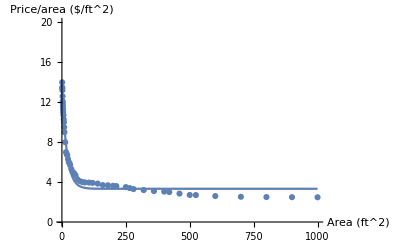

```mathematica
Normal[model1]
Show[Plot[model1[x],{x,0,1000},PlotRange->{0,20}],ListPlot[SingleStickerPricingData],AxesLabel->{"Area (ft^2)","Price/area ($/ft^2)"}]
```

This model does not do what we want, so try again, this getting rid of the constant c.

| Estimate | Standard Error | t-Statistic | P-Value
A | 11.3743 | 0.575321 | 19.7703 | 1.44466×10^-25
beta | 0.013005 | 0.0021052 | 6.17757 | 1.07982×10^-7

11.3743 ⅇ^(-0.013005 x)

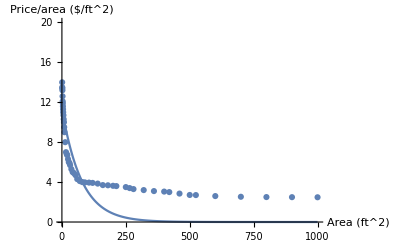

```mathematica
model2=NonlinearModelFit[SingleStickerPricingData,A Exp[-beta*x] ,{A,beta},x];
model2["ParameterTable"]
Normal[model2]
Show[Plot[model2[x],{x,0,1000},PlotRange->{0,20}],ListPlot[SingleStickerPricingData],AxesLabel->{"Area (ft^2)","Price/area ($/ft^2)"}]
```

This isn’t what we want, either. Try again, this time raising x to some exponent.

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

| Estimate | Standard Error | t-Statistic | P-Value
A | 0.000238827 | 0.00264976 | 0.0901315 | 0.928543
beta | -11.1107 | 11.079 | -1.00285 | 0.32076
c | -0.0267728 | 0.0287197 | -0.932208 | 0.355709

0.000238827 ⅇ^(11.1107/x^0.0267728)

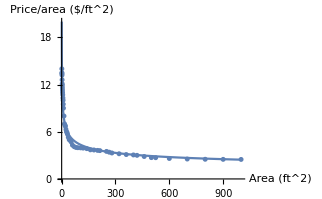

```mathematica
model3=NonlinearModelFit[SingleStickerPricingData,A Exp[-beta*(x^c)],{A,beta,c},x];
model3["ParameterTable"]
Normal[model3]
Show[Plot[model3[x],{x,0,1000},PlotRange->{0,20}],ListPlot[SingleStickerPricingData],AxesLabel->{"Area (ft^2)","Price/area ($/ft^2)"}]
```

This regression fails to converge, but gives us a good idea of what the parameters should be. We will try plotting these rough estimates.

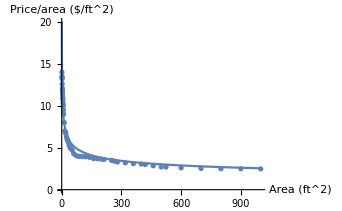

```mathematica
A0=0.00022;
beta0 = -11.2;
c0 = -0.026;
price[x_]:=A0 Exp[-beta0*(x^c0)];

Show[Plot[price[x],{x,0,1000},PlotRange->{0,20}],ListPlot[SingleStickerPricingData],AxesLabel->{"Area (ft^2)","Price/area ($/ft^2)"}]
```

This isn’t a good model, since it is hypersensitive to each of its parameters and responds in unintuitive ways, so it isn’t easy to make pricing changes. Try a model that is not exponential.

| Estimate | Standard Error | t-Statistic | P-Value
A | 18.5167 | 0.281194 | 65.8502 | 5.19518×10^-51
r | -0.317688 | 0.00598635 | -53.0687 | 2.67483×10^-46

18.5167/(1+x)^0.317688

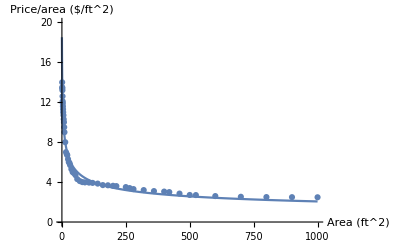

```mathematica
model4=NonlinearModelFit[SingleStickerPricingData,A (1+x)^r,{A,r},x];
model4["ParameterTable"]
Normal[model4]
Show[Plot[model4[x],{x,0,1000},PlotRange->{0,20}],ListPlot[SingleStickerPricingData],AxesLabel->{"Area (ft^2)","Price/area ($/ft^2)"}]
```

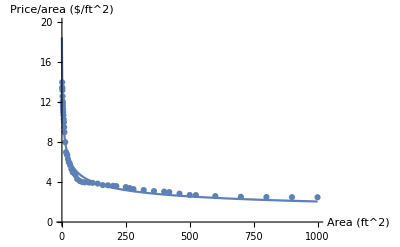

```mathematica
A0=18.5;
r0 = -.318;
price[x_]:=A0 (1+x)^r0;

Show[Plot[price[x],{x,0,1000},PlotRange->{0,20}],ListPlot[SingleStickerPricingData],AxesLabel->{"Area (ft^2)","Price/area ($/ft^2)"}]
```

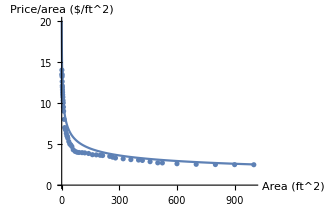

```mathematica
A0=20;
r0 = -.3;
price[x_]:=A0 (1+x)^r0;

Show[Plot[price[x],{x,0,1000},PlotRange->{0,20}],ListPlot[SingleStickerPricingData],AxesLabel->{"Area (ft^2)","Price/area ($/ft^2)"}]
```

This model is much better since it is simpler and responds intuitively to changes in the constant A. Some additional notes are that this model is only valid for the regime in which order area > 1 sq-ft since as order square footage becomes very small, the minimum order requirements come into play.

Now, we must fit the data for the sheet stickers. I again begin by loading that data.

```mathematica
SheetStickerPricingData = {{0,20},{1,18},{1.3,17.7},{1.6,17.3},{2,17},{2.5,16.8},{3,16.2},{3.5,15.6},{4,15},{4.5,13},{5,12},{6,11},{7,10.5},{8,10},{9,9.8},{10,9.5},{13,9.2},{16,9},{19,8.5},{21,8},{24,7.8},{27,7.5},{30,7.4},{32,7.3},{37,7.1},{42,7},{47,6.9},{53,6.7},{60,6.4},{70,6.1},{80,6},{90,5.5},{106,5},{120,4.8},{140,4.55},{160,4.5},{180,4.45},{200,4.4},{213,4.2},{250,4.1},{265,4},{280,3.7},{320,3.6},{360,3.58},{400,3.54},{420,3.5},{460,3.3},{500,3.25},{524,3.2},{600,3.18},{700,3.09},{800,3},{900,2.97},{1000,2.95}};
```

I will guess a model of the similar form to the last.

| Estimate | Standard Error | t-Statistic | P-Value
A | 22.2496 | 0.393215 | 56.5837 | 2.18485×10^-48
r | -0.311377 | 0.00729174 | -42.7027 | 3.65309×10^-42

22.2496/(1+x)^0.311377

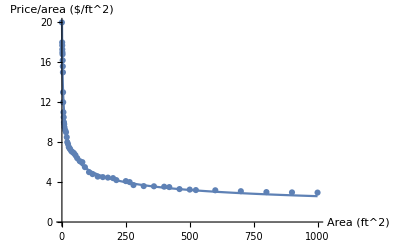

```mathematica
model5=NonlinearModelFit[SheetStickerPricingData,A (1+x)^r,{A,r},x];
model5["ParameterTable"]
Normal[model5]
Show[Plot[model5[x],{x,0,1000},PlotRange->{0,20}],ListPlot[SheetStickerPricingData],AxesLabel->{"Area (ft^2)","Price/area ($/ft^2)"}]
```

This guess ended up working quite well. Let’s tweak the parameters now.

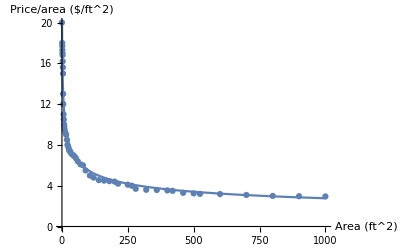

```mathematica
A0=22;
r0 = -0.3;
price[x_]:=A0  (1+x)^r0;

Show[Plot[price[x],{x,0,1000},PlotRange->{0,20}],ListPlot[SheetStickerPricingData],AxesLabel->{"Area (ft^2)","Price/area ($/ft^2)"}]
```

So with that, we have a function for price depending on area ordered for both kinds of stickers.

Edit: The single sticker pricing model didn’t behave quite as we wanted. We want to enforce the end behavior to asymptotically approach $2.75 $/ft^2 and for the mid-range pricing to be lower (making the function more convex). I will add an asymptote to the model and also allow the convexity to vary with x in a linear fashion.

```mathematica
Clear[B,H,r,x, gamma];
```

| Estimate | Standard Error | t-Statistic | P-Value
B | 15.4921 | 0.506684 | 30.5755 | 5.02369×10^-34
r | -0.367434 | 0.0221012 | -16.6251 | 5.19541×10^-22
gamma | 0.00239659 | 0.000407891 | 5.87556 | 3.4145×10^-7

2.75+15.4921 (1+x)^(-0.367434-0.00239659 x)

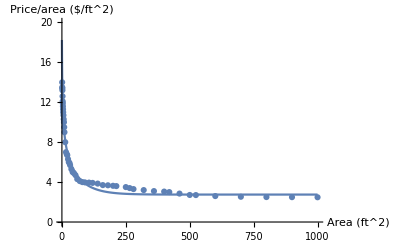

```mathematica
model6=NonlinearModelFit[SingleStickerPricingData,2.75+B (1+x)^(r-gamma x),{B,r, gamma},x];
model6["ParameterTable"]
Normal[model6]
Show[Plot[model6[x],{x,0,1000},PlotRange->{0,20}],ListPlot[SingleStickerPricingData],AxesLabel->{"Area (ft^2)","Price/area ($/ft^2)"}]
```

2.75+18 (1+x)^(-0.45-0.0005 x)

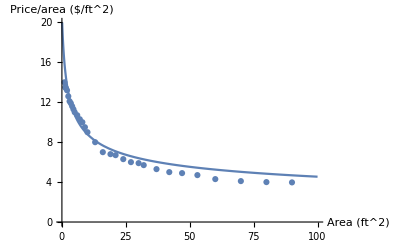

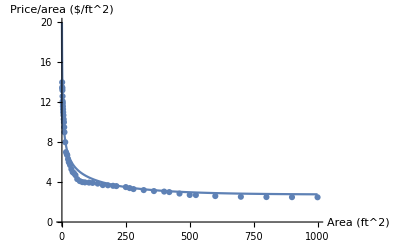

```mathematica
B=18;
H=2.75;
r=-0.45;
gamma=0.0005;
price[x_]:=H+B (1+x)^(r-gamma x);

Normal[price[x]]
Show[Plot[price[x],{x,0,100},PlotRange->{0,20}],ListPlot[SingleStickerPricingData],AxesLabel->{"Area (ft^2)","Price/area ($/ft^2)"}]
Show[Plot[price[x],{x,0,1000},PlotRange->{0,20}],ListPlot[SingleStickerPricingData],AxesLabel->{"Area (ft^2)","Price/area ($/ft^2)"}]
```

Let’s test some points in this new model.

```mathematica
price[0]
price[200]
price[1000]
price[10000]
```

20.75

3.7239

2.7754

2.75

This looks about right, so let’s try to extend this model to the sheet sticker pricing.

```mathematica
B=22;
H=2.5;
r=-0.4;
gamma=0.0004;
price[x_]:=H+B (1+x)^(r-gamma x);
```

2.5+22 (1+x)^(-0.4-0.0004 x)

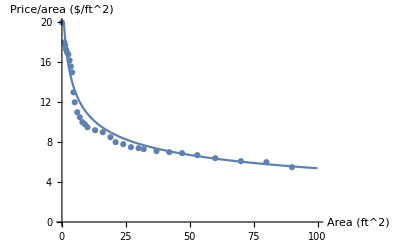

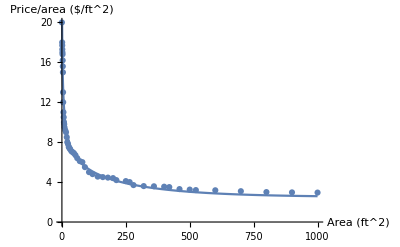

```mathematica
Normal[price[x]]
Show[Plot[price[x],{x,0,100},PlotRange->{0,20}],ListPlot[SheetStickerPricingData],AxesLabel->{"Area (ft^2)","Price/area ($/ft^2)"}]
Show[Plot[price[x],{x,0,1000},PlotRange->{0,20}],ListPlot[SheetStickerPricingData],AxesLabel->{"Area (ft^2)","Price/area ($/ft^2)"}]
```

```mathematica
price[0]
price[20]
price[100]
```

24.5

8.85268

5.3875